On p17 of TAOCP F6. Donald Knuth shows a sequence of frames from Conways game of Life that end with the alive cells forming the letters LIFE.

In the next few paragraphs he describes how this is achieved.

He states that 190 clauses are needed for each cell for each transition T.

He does not provide these clauses.

I am exploring this section as part of an undergrad math project. I would love to be able to code up this example and get the game of life to write other words besides LIFE.

I wish Knuth had provided these clauses as I find it difficult to infer them from his implicit description of them.

Has anyone managed to write these clauses down?

Here are screen shots of the section: and a link to a pdf of a preprint of the book.

## using a SAT solver to make Conways Game of Life write Characters and Words!

Here I have tried to formulate a simpler version of the problem Knuth describes.

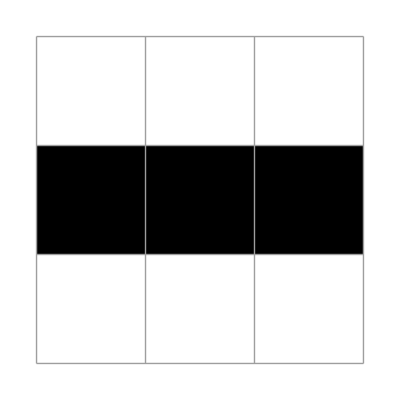
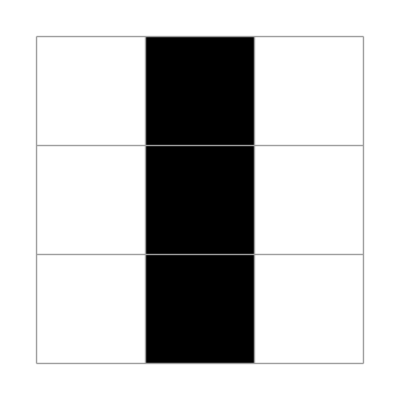

```mathematica
X1=({{0, 0, 0}, {1, 1, 1}, {0, 0, 0}});
plt/@NestList[updateLife[{3,3}][ #]&,
X1,1]
```

find a sequence that ends in

(x_211 | x_212 | x_213
x_221 | x_222 | x_223
x_231 | x_232 | x_233)=(0 | 1 | 0
0 | 1 | 0
0 | 1 | 0)

(x_111 | x_112 | x_113
x_121 | x_122 | x_123
x_131 | x_132 | x_133)=(? | ? | ?
? | ? | ?
? | ? | ?)

X_2=(x_111 | x_112 | x_113
x_121 | x_122 | x_123
x_131 | x_132 | x_133)

X_1=(x_211 | x_212 | x_213
x_221 | x_222 | x_223
x_231 | x_232 | x_233)

F[X_1,X_2]=?

I need to write some Boolean formula in terms of these Boolean variables. that encodes the rule of the Game of Life.